# Precipitation Predictability over Extended Lead Time for West Coast United States

BX Pan
2017.10.22

## Background

The Quiet Revolution of Numerical Weather Prediction

#### ECMWF

```mathematica
ECMWF=Labeled[ImageResize[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Refer/RevolutionOfECMWF.png"],
		1000],
	"Fig1. Predictability(Correlation) of Extratropical 500hpa GPH from ECMWF,  Bauer, etc. Nature, 2015",Bottom]
```

-Graphics-Fig1. Predictability(Correlation) of Extratropical 500hpa GPH from ECMWF,  Bauer, etc. Nature, 2015

#### NCEP CFS

```mathematica
NCEP=Labeled[ImageResize[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Refer/RevolutionOfNCEP.png"],
		1000],
	"Fig2. Predictability(Mean Error) of North America 500hpa GPH from NCEP,  NCEP Central Operations, March, 2016",Bottom]
```

-Graphics-Fig2. Predictability(Mean Error) of North America 500hpa GPH from NCEP,  NCEP Central Operations, March, 2016

#### Earth Observation Satellites

```mathematica
satellites=Block[{data,primary,changestyle},
	data=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Refer/Satellites/ListofSatellites.xlsx"];
	primary=data[[1]][[2;;]];
	primary=Select[primary[[;;,{1,3,4,6}]],#[[2]]≠"TBD"&];
	changestyle[string_]:=If[Not[StringQ[string]],
						{IntegerPart[string],1,1},
						If[StringTake[string,1]=="≥",
							ToExpression[{StringTake[string,2;;],1,1}],
							ToExpression[{StringTake[string,1;;4],
								              StringTake[string,6;;7],
								              StringTake[string,9;;10]}]]];
	Sort[Map[{#[[1]],changestyle[#[[2]]],changestyle[#[[3]]],
	If[StringTake[#[[4]],-1]=="\n",StringTake[#[[4]],1;;-2],#[[4]]]}&,primary],#2[[2,1]]≥#1[[2,1]]&]];
allmissions=Labeled[TimelinePlot[Map[Association[Rule[#[[1]]<>"("<>#[[4]]<>")",Interval[{#[[2]],#[[3]]}]]]&,satellites[[1;;672;;5]]],
	BaseStyle->8,
	ImageSize->1200,
	FrameLabel->Map[Style[#,FontSize->25]&,{"Time","Satellite Missions"}],
	FrameTicksStyle->Directive[Black,25],
	Frame->True],Style["1/5 of the total 672 Earth Science Satellites",FontSize->25],Top]
```

-Graphics-1/5 of the total 672 Earth Science Satellites

-Graphics-1/5 of the total 672 Earth Science Satellites

```mathematica
long=Block[{longlives},
longlives=DeleteDuplicates[Flatten[Block[{duration=Map[#[[3,1]]-#[[2,1]]&,satellites],sort},
	sort=Sort[duration,#1>=#2&];
	Map[Position[duration,#]&,sort[[1;;10]]]]]];
TableForm[Map[{satellites[[#,1]],satellites[[#,4]],DateObject[satellites[[#,2]]],
		DateObject[satellites[[#,3]]],
		IntegerPart[DateDifference[satellites[[#,2]],satellites[[#,3]],"Year"]]}&,longlives],
	TableHeadings->{None, {"Mission","Organization","Launch Date","Deoperation Date","Duration"}}]]
```

Mission | Organization | Launch Date | Deoperation Date | Duration
Diadéme-1 | CNES | Day: Wed 8 Feb 1967 | Day: Sat 1 Jan 2050 | 82 yr
Diadéme-2 | CNES | Day: Wed 15 Feb 1967 | Day: Sat 1 Jan 2050 | 82 yr
STARLETTE | CNES | Day: Thu 6 Feb 1975 | Day: Sat 1 Jan 2050 | 74 yr
STELLA | CNES | Day: Thu 30 Sep 1993 | Day: Sat 1 Jan 2050 | 56 yr
LAGEOS-1 | ASI
NASA | Day: Tue 4 May 1976 | Day: Sun 1 Jan 2017 | 40 yr
LAGEOS-2 | ASI
NASA | Day: Thu 22 Oct 1992 | Day: Thu 1 Jan 2032 | 39 yr
Landsat-5 | USGS
NASA | Day: Thu 1 Mar 1984 | Day: Fri 18 Nov 2011 | 27 yr
GEOTAIL | JAXA
NASA | Day: Thu 2 Jul 1992 | Day: Sun 1 Jan 2017 | 24 yr
SCD-1 | INPE | Day: Tue 9 Feb 1993 | Day: Sun 1 Jan 2017 | 23 yr
WIND | NASA | Day: Tue 1 Nov 1994 | Day: Sun 1 Jan 2017 | 22 yr

For Scientific Exploration Purposes:

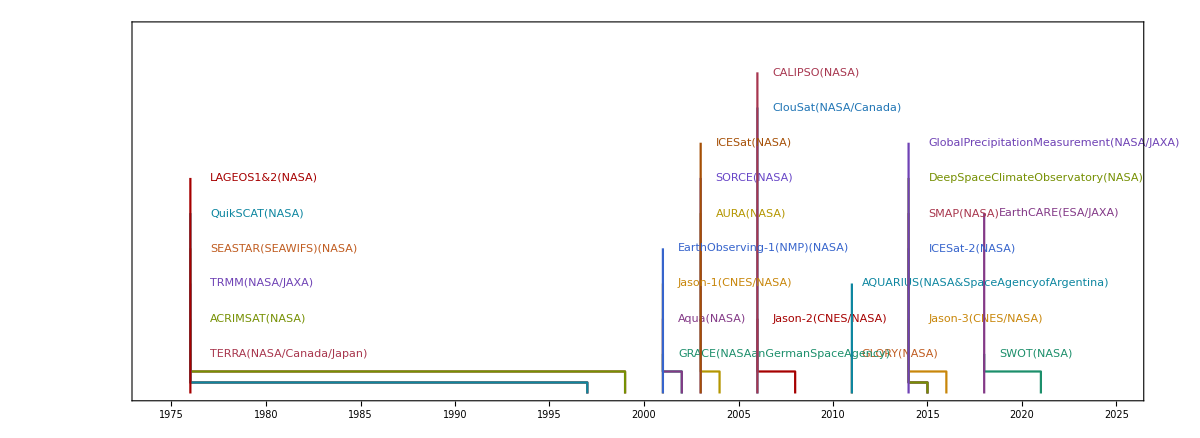

```mathematica
satellites=Block[{data=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Refer/satellites.txt","Table"]},
	Sort[data[[;;,{1,3,4}]],#2[[3]]≥#1[[3]]&]];
TimelinePlot[Map[Association[Rule[#[[1]]<>"("<>#[[2]]<>")",{#[[3]],1,1}]]&,satellites],
	BaseStyle->12,
	ImageSize->1200,
	Frame->True]
```

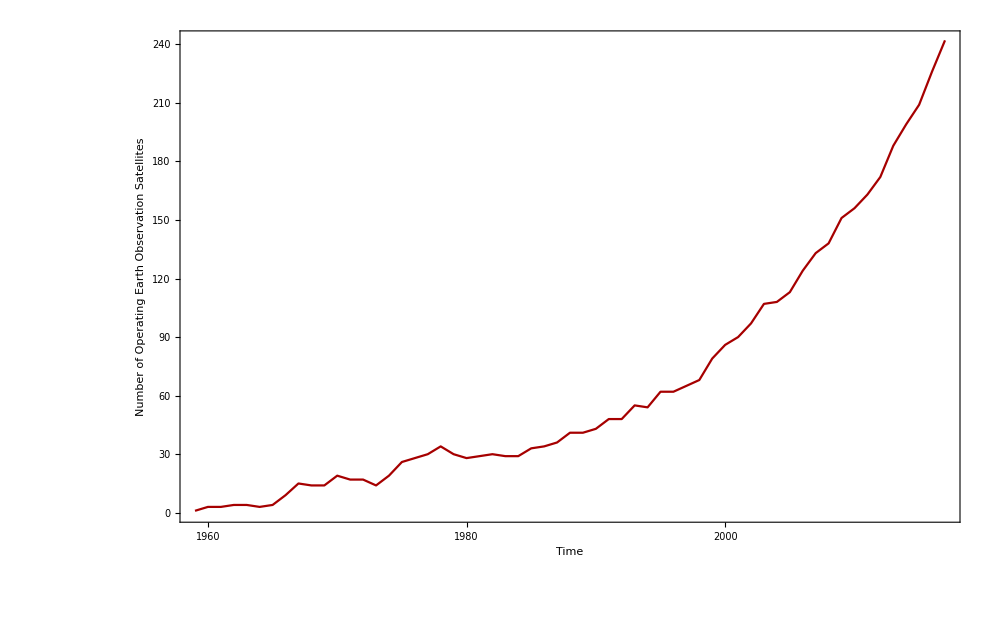

```mathematica
years=Range[1959,2017];
result=Table[Total[Map[If[And[years[[i]]≥#[[2,1]],years[[i]]≤#[[3,1]]],1,0]&,satellites]],
	{i,Length[years]}];
DateListPlot[TimeSeries[result,{{1959,1,1},Automatic,"Year"}],
	BaseStyle->25,
	ImageSize->1000,
	FrameLabel->{"Time","Number of Operating Earth Observation Satellites"}]
```

The Ongoing Inquiry of the Foundation of “Climate Projection”

```mathematica
TableForm[{{"Initial Value Problem","Deterministic"},
           {"Boundary Value Problem","Proabilisitc"}},
          TableHeadings->{{"Weather Forecast","Climate Prediction"},None}]
```

Weather Forecast | Initial Value Problem | Deterministic
Climate Prediction | Boundary Value Problem | Proabilisitc

A deterministic system could be unpredictable:

Is the earth’s weather system ergodic?

If it was ergodic, will an imperfect model be a valid predictor for the climate’s statistical features?

The Emerging Demand for Accurate and Extended Quantitative Precipitation Forecast(QPF)

```mathematica
Labeled[ImageResize[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Refer/DemandForS2S.png"],1000],
	 "Demand For Accurate and Extended QPF, modified from the Earth System Prediction Capability Office.",Bottom]
```

-Graphics-Demand For Accurate and Extended QPF, modified from the Earth System Prediction Capability Office.

On the Long Term Prediction of Chaotic System--Example of Lorenz System

The Lorenz System is derived from the Oberbeck-Boussinesq Approximation to the equations describing fluid circulation in a shallow layer of fluid, heated uniformly from below and cooled uniformly from above. This fluid circulation is known as Rayleigh-Bénard Convection. The fluid is assumed to circulate in two dimensions (vertical and horizontal) with periodic rectangular boundary conditions(Wikipedia).

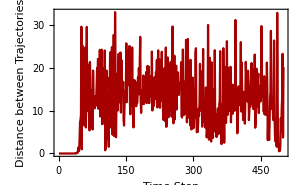
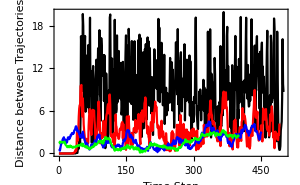
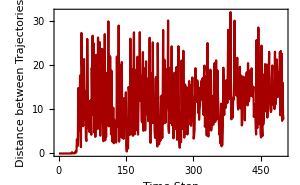
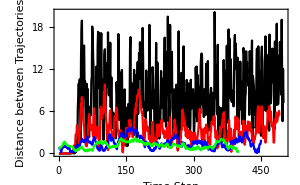
| Trajectory_1 | Trajectory_2 | L2 Distance | L2 Distance of Temporal Mean
{0, 1, 1} | -Graphics3D- | -Graphics3D- | -Graphics- | -Graphics-
{-10, 10, 10} | -Graphics3D- | -Graphics3D- | -Graphics- | -Graphics-Lorenz System Simulations by Pertubating y_0 of 1/10000000000

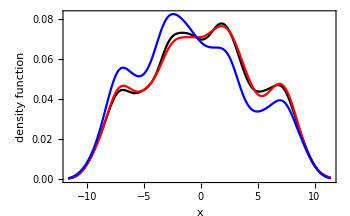
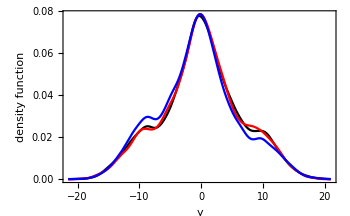
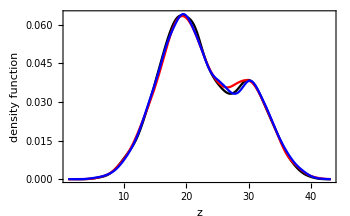

Subseasonal to Seasonal(S2S) Prediction Project (2013-2018)

The division between weather and climate is artificial and needs to be re-delineate as lead time of weather forecast models stretches forward and climate models backward. 
The motivation of S2S is to improve forecast skill and understanding on the sub-seasonal to seasonal time scale, and promote its uptake by operational centres and exploitation by the applications community.

```mathematica
wwrp=ImageCrop[-Graphics-];
wcrp=ImageCrop[-Graphics-];
GraphicsRow[Map[ImageCrop,{wwrp,wcrp}],ImageSize->Full]
```

-Graphics-

Could “S2S forecasts be as widely used a decade from now as weather forecasts are today”?

## Specify the Research Questions

#### Spotlights regarding S2S Predictability Evaluation

El Niño–Southern Oscillation (ENSO)

```mathematica
nino34=-Graphics-;
nino12=-Graphics-;
nino4=-Graphics-;
nino3=-Graphics-;
GraphicsGrid[ArrayReshape[Map[ImageResize[ImageCrop[#],500]&,{nino12,nino3,nino34,nino4}],
	{2,2}],ImageSize->1200,Spacings->{0,-60}]
```

-Graphics-

Madden–Julian oscillation (MJO)

Capacity to Predict MJO (average gain of 1 day of prediction skill per year for ECMWF)

MJO prediction using the sub-seasonal to seasonal forecast model of Beijing Climate Center

Outcomes and challenges of global high-resolution non-hydrostatic atmospheric simulations using the K computer

Teleconnection between MJO and extratropics

MJO-related tropical convection anomalies lead to more accurate stratospheric vortex variability in subseasonal forecast models

Sudden Stratospheric Warming

Circulation Pattern

Effects of air-sea interaction on extended-range prediction of geopotential height at 500 hPa over the northern extratropical region

Simulations of Asian Summer Monsoon in the Sub-seasonal to Seasonal Prediction Project (S2S) database

Extremes

Long-lead prediction of the 2015 fire and haze episode in Indonesia

Subseasonal Dynamical Prediction of East Asian Cold Surges

Subseasonal prediction of the heat wave of December 2013 in Southern South America by the POAMA and BCC-CPS models

Tropical Cyclones

Prospects for subseasonal forecast of Tropical Cyclone statistics with the CFS

Extratropical Storm Tracks

Advancing Atmospheric River Forecasts into Subseasonal-to-Seasonal Timescales

Seasonal Noise Versus Subseasonal Signal: Forecasts of California Precipitation During the Unusual Winters of 2015–2016 and 2016–2017

Predictability for extratropical and tropical areas are different, due to different precipitation mechanisms.

```mathematica
ImageResize[xkcdConvert[ListLinePlot[{{{1,0.86},{2,0.85},{3,0.75},{4,0.7},{5,0.65},{7,0.5},{10,0.3},{12,0.13},{14,0.13},{20,0.135},{30,0.2}},
              {{1,0.7},{2,0.65},{4,0.5},{7,0.45},{14,0.4},{20,0.42},{30,0.43}}},
              PlotStyle->{Blue,Red},
              Frame->True,
              Ticks->None,
              FrameLabel->{"Forecast Leading Days","Predictability"},
              Epilog -> 
   xkcdLabel /@ {{"Extratropic", {3, 0.75}, {1, 0}}, {"Tropic", {4, 0.5}, {0, -0.3}}}]],700]
```

-Graphics-

Extratropical predictability is mostly derived from synoptic-scale atmospheric dynamics

Tropical predictability is primarily derived from the response of moist convection to
slowly varying forcing such as from ENSO.

#### Study Area

```mathematica
fig1=GeoGraphics[{EdgeForm[Red], GeoStyling["ReliefMap"], 
			Polygon[LinguisticAssistant],
			Polygon[GeoPosition[Import["/Users/lambda/Documents/S2S/Results/Polygons/oregon.mx"]]],
			Polygon[GeoPosition[Import["/Users/lambda/Documents/S2S/Results/Polygons/washington.mx"]]]},
			Frame->True,
			BaseStyle->28,
			ImageSize->800,
			GridLines->Automatic,
			AspectRatio->1,
			GeoGridLines->True,
			FrameLabel->{"Longitude","Latitude"},
			GeoRange->{{32,50.},{-130,-110}},
			GeoProjection->"Equirectangular"]
```

-Graphics-

### Economical Reason

```mathematica
economic=Transpose[{{"California",39.25,"12.1%",13.8,"1.7%",7549,"13.6%"},
           {"Oregon",4.09,"1.3%",31.3,"3.9%",1554,"2.8%"},
           {"Washington",7.29,"2.3%",73.4,"9.2%",1623,"2.9%"}}];
source=Style["Population data from Data from U.S. Census BureauLast updated: Jun 15, 2017;
Hydroelectric data from U.S. Energy Information Administration, 2015 report;
Irrigation data from 2012 Census of Agriculture, USDA, National Agricultural Statistics Service.",FontSize->15];
Labeled[TableForm[economic[[2;;]],TableHeadings->{{"Population","(million)",
										  "Annual Hydroelectric Consumption","(billion KW·h)",
										  "Irrigated Farm Area","(thousand Acres)"},
							economic[[1,;;]]},TableAlignments->Center],source,Bottom]
```

| California | Oregon | Washington
Population | 39.25 | 4.09 | 7.29
(million) | 12.1% | 1.3% | 2.3%
Annual Hydroelectric Consumption | 13.8 | 31.3 | 73.4
(billion KW·h) | 1.7% | 3.9% | 9.2%
Irrigated Farm Area | 7549 | 1554 | 1623
(thousand Acres) | 13.6% | 2.8% | 2.9%Population data from Data from U.S. Census BureauLast updated: Jun 15, 2017;
Hydroelectric data from U.S. Energy Information Administration, 2015 report;
Irrigation data from 2012 Census of Agriculture, USDA, National Agricultural Statistics Service.

### Physical Reason

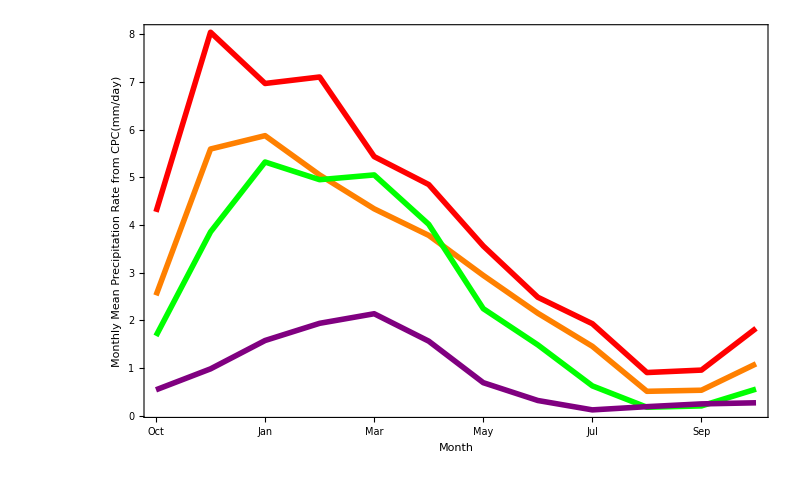

```mathematica
precip=Import["/Users/lambda/Downloads/precip.V1.0.mon.1981-2010.ltm.nc",{"Datasets","precip"}];
lat=Import["/Users/lambda/Downloads/precip.V1.0.mon.1981-2010.ltm.nc",{"Datasets","lat"}];
lon=Import["/Users/lambda/Downloads/precip.V1.0.mon.1981-2010.ltm.nc",{"Datasets","lon"}];
grid=Table[Table[{lon[[j]],lat[[i]]},{j,Length[lon]}],{i,Length[lat]}];

<<"/Users/lambda/Documents/Mathematica/ToolBox/Cut.m"

NCA=Import["/Users/lambda/Documents/Data/GeoDivision/CONUS/northCalifornia.mx"];
SCA=Import["/Users/lambda/Documents/Data/GeoDivision/CONUS/southCalifornia.mx"];
OR=Import["/Users/lambda/Documents/Data/GeoDivision/CONUS/oregon.mx"];
OR=Polygon[Map[Map[{#[[2]]+360,#[[1]]}&,#]&,OR]];
WA=Import["/Users/lambda/Documents/Data/GeoDivision/CONUS/washington.mx"];
WA=Polygon[Map[Map[{#[[2]]+360,#[[1]]}&,#]&,WA]];
SCAgrids=Cut[Flatten[grid,1],SCA[[1]]];
NCAgrids=Cut[Flatten[grid,1],{NCA[[1]]}];
ORgrids=Cut[Flatten[grid,1],OR[[1]]];
WAgrids=Cut[Flatten[grid,1],WA[[1]]];
SCAprecip=Map[Flatten[{#[[10;;12]],#[[1;;9]]}]&,Map[precip[[;;,#[[1]],#[[2]]]]&,Map[Position[grid,#][[1]]&,SCAgrids]]];
NCAprecip=Map[Flatten[{#[[10;;12]],#[[1;;9]]}]&,Map[precip[[;;,#[[1]],#[[2]]]]&,Map[Position[grid,#][[1]]&,NCAgrids]]];
ORprecip=Map[Flatten[{#[[10;;12]],#[[1;;9]]}]&,Map[precip[[;;,#[[1]],#[[2]]]]&,Map[Position[grid,#][[1]]&,ORgrids]]];
WAprecip=Map[Flatten[{#[[10;;12]],#[[1;;9]]}]&,Map[precip[[;;,#[[1]],#[[2]]]]&,Map[Position[grid,#][[1]]&,WAgrids]]];
Labeled[Show[{ListLinePlot[Mean[WAprecip],PlotStyle->{Red,Thickness[0.005]}],
	  ListLinePlot[Mean[ORprecip],PlotStyle->{Orange,Thickness[0.005]}],
	  ListLinePlot[Mean[NCAprecip],PlotStyle->{Green,Thickness[0.005]}],
	  ListLinePlot[Mean[SCAprecip],PlotStyle->{Purple,Thickness[0.005]}]
	  },
	  PlotRange->{{1.,12},Automatic},
	  BaseStyle->25,
	  Frame->True,
	  FrameLabel->{"Month","Monthly Mean Precipitation Rate from CPC(mm/day)"},
	  ImageSize->800,
	  FrameTicks->{{Automatic,None},{{{1,"Oct"},{3,"Jan"},{5,"Mar"},{7,"May"},{9,"Jul"},
	  {11,"Sep"}},None}}
	  ],LineLegend[{Purple,Green,Orange,Red},{"SCA","NCA","OR","WA"},LegendLayout->"Row"],Bottom]
```

Research Questions

The accuracy and extension of current QPF capacity for the West Coast United States?

Is there any forecast windows?

## Materials

GCMs

```mathematica
datasets=Block[{model,primary,size,frequency},
	SetDirectory["/Users/lambda/Documents/Research/3_S2SEvaluation/Data"];
	models=Select[FileNames[],StringFreeQ[#,"."]&];
	primary={
		{Green,"BoM",LinguisticAssistant,"T47L17"},    
		{Red,"CMA",LinguisticAssistant,"T106L40"},  
		{Purple,"StyleBox[\"ECCC\",FontWeight->\"Bold\"]",LinguisticAssistant,"0.45^°×0.45^°L40"}, 
		{Gray,"StyleBox[\"ECMWF\",FontWeight->\"Bold\"]",LinguisticAssistant,"Tco639/319L91"},
		{Magenta,"StyleBox[\"HMCR\",FontWeight->\"Bold\"]",LinguisticAssistant,"1.1^°×1.4^°L28"},   
		{Yellow, "ISAC-CNR",LinguisticAssistant,"0.75^°×0.56^°L54"}, 
		{LightPurple,"JMA", LinguisticAssistant,"T1479/T1319L100"},
		{Brown, "StyleBox[\"KMA\",FontWeight->\"Bold\"]",LinguisticAssistant,"N216L85"},  
		{Cyan,"Météo-France",LinguisticAssistant,"T255L91"},  
		{Blue,"NCEP",LinguisticAssistant,"T126L64"},
		{Orange, "StyleBox[\"UKMO\",FontWeight->\"Bold\"]",LinguisticAssistant,"N216L85"}};
	size=Map[Block[{data=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Data/"<>#<>"/"<>#<>".mx"]},
		Dimensions[data[[1]]]][[{1,3}]]&,models];
	frequency=Block[{time,f,e},
		time=Map[Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Data/"<>#<>"/"<>#<>"_control_time.mx"]&,models];
		f=Map[Round[#[[1]],0.1]&,Map[(DateDifference[#[[1]],#[[-1]]])/(Length[#]+0.0)&,time]];
		e=Map[{#[[1,1]],#[[-1,1]]}&,time];
		Map[If[#[[1]]<1.01,
		"Every day from "<>ToString[#[[2,1]]]<>" to "<>ToString[#[[2,2]]],
		"Every "<>ToString[#[[1]]]<>" days from "<>ToString[#[[2,1]]]<>" to "<>ToString[#[[2,2]]]]&,Transpose[{f,e}]]];
	Map[Flatten,Transpose[{primary,size,frequency}]]];
label=Style[TableForm[Map[Flatten[{#[[1]],#[[2]]<>"("<>ToString[#[[3]][[2]]]<>")",#[[4;;]]}]&,datasets],
	TableHeadings->{None,{"","Model","Resolution","Ensemble Size","Extension(day)","Hincast Frequency"}},
	TableAlignments->Left],FontSize->18];
Labeled[Show[GeoRegionValuePlot[Map[#[[3]]->#[[1]]&,datasets]],
	  GeoRegionValuePlot[Map[#[[3]]->#[[1]]&,datasets[[{6,9,11}]]]],ImageSize->1260],
	  label,Bottom]
(*Export["/Users/lambda/Documents/Research/3_S2SEvaluation/Results/fig1_dataset.pdf",%];*)
```

-Graphics- | Model | Resolution | Ensemble Size | Extension(day) | Hincast Frequency
RGBColor[0, 1, 0] | BoM(Australia) | T47L17 | 33 | 62 | Every 5.1 days from 1981 to 2013
RGBColor[1, 0, 0] | CMA(China) | T106L40 | 4 | 60 | Every day from 1994 to 2014
RGBColor[0.5, 0, 0.5] | ECCC(Canada) | 0.45^°×0.45^°L40 | 4 | 32 | Every 4.1 days from 1995 to 2014
GrayLevel[0.5] | ECMWF(Europe) | Tco639/319L91 | 11 | 46 | Every 2.6 days from 1995 to 2016
RGBColor[1, 0, 1] | HMCR(Russia) | 1.1^°×1.4^°L28 | 10 | 61 | Every 2.9 days from 1985 to 2010
RGBColor[1, 1, 0] | ISAC-CNR(Italy) | 0.75^°×0.56^°L54 | 1 | 31 | Every 5. days from 1981 to 2010
RGBColor[0.94, 0.88, 0.94] | JMA(Japan) | T1479/T1319L100 | 5 | 34 | Every 10.1 days from 1981 to 2010
RGBColor[0.6, 0.4, 0.2] | KMA(SouthKorea) | N216L85 | 3 | 60 | Every 10.9 days from 1991 to 2010
RGBColor[0, 1, 1] | Météo-France(France) | T255L91 | 15 | 61 | Every 15.2 days from 1993 to 2014
RGBColor[0, 0, 1] | NCEP(UnitedStates) | T126L64 | 4 | 44 | Every day from 1999 to 2010
RGBColor[1, 0.5, 0] | UKMO(UnitedKingdom) | N216L85 | 3 | 60 | Every 7.6 days from 1993 to 2015

#### About GCM resolution

```mathematica
Block[{a=-Graphics-,b=-Graphics-},
GraphicsRow[{a,b},ImageSize->1000]]
```

-Graphics-

Observations

#### CPC Gauge Based Precipitation

Daily Data Covering CONUS, 0.25^°×0.25^°, from 1948.1.1 to 2017.8.13

## Skill Metric

Deterministic Metrics

Ensemble mean is taken as deterministic simulation. Its discrepancy with observation is quantified using the following skill metrics.

#### Pearson Correlation Coefficient(r)

```mathematica
"r=(Cov (simu, obser))/σ_simu"
```

r=(Cov (simu, obser))/σ_simu

#### Root Mean Square Error(RMSE)

```mathematica
"RMSE=√((Σ SuperscriptBox[(simu - obser), 2])/n)"
```

RMSE=√((Σ SuperscriptBox[(simu - obser), 2])/n)

#### Nash Sutcliffe Efficiency(NSE)

```mathematica
"NSE=1-(Σ SuperscriptBox[(simu - obser), 2])/(Σ SuperscriptBox[(obser - OverscriptBox[obser, _]), 2])"
```

NSE=1-(Σ SuperscriptBox[(simu - obser), 2])/(Σ SuperscriptBox[(obser - OverscriptBox[obser, _]), 2])

Probabilistic Metrics

Each ensemble member is taken as a potential realization of future weather, together they construct the probability distribution of the future(even though there is only one realized future). The probabilistic metrics measure the entropy of the conditional distribution.

#### Receiver Operating Characteristic(ROC) Score

```mathematica
pdf=Plot3D[PDF[MultinormalDistribution[{8, 7.5}, {{8, 0.65}, {0.65, 6.5}}], {x, 
y}], {x, 0, 12}, {y, 0, 12},
	PlotRange->Full,
	BaseStyle->15,
	ImageSize->500,
	AxesLabel->{"Observation","Simulation",Rotate["P.D.F",Pi/2]}];
hitrate=BarChart[{1,2,3,2,1,2.5},
	BaseStyle->15,
	ImageSize->500,
	Frame->True,
	FrameLabel->{"Simulation","P.D.F"},
	FrameTicks->{{None,None},{{{1,"1-2"},{2,"3-4"},{3,"5-6"},{4,"7-8"},{5,"9-10"},{6,"11-12"}},None}},
	ChartStyle->{Red,Red,Blue,Red,Red},
	PlotLabel->"P.D.F. of Simulation conditioned on that\n Observation is within [5,6]"
	];
falsealarm=BarChart[{2,1.5,3,2.5,1,0.4},
	BaseStyle->15,
	ImageSize->500,
	Frame->True,
	FrameLabel->{"Simulation","P.D.F"},
	FrameTicks->{{None,None},{{{1,"1-2"},{2,"3-4"},{3,"5-6"},{4,"7-8"},{5,"9-10"},{6,"11-12"}},None}},
	ChartStyle->{Green,Green,Orange,Green,Green},
	PlotLabel->"P.D.F. of Simulation conditioned on that\n Observation is out of [5,6]"
	];
label=TableForm[{{Style["Hit",Blue],Style["Miss",Red]},
	       {Style["False Alarm",Orange],Style["Correct Reject",Green]}},
	TableHeadings->{{"obser=1","obser=0"}, {"simu=1","simu=0"}}];
Labeled[GraphicsRow[{pdf,hitrate,falsealarm},Spacings->-50],label,Bottom]
```

-Graphics- | simu=1 | simu=0
obser=1 | Hit | Miss
obser=0 | False Alarm | Correct Reject

For each P.D.F. bin, the hit ratio and false alarm ratio can be calculated(they does not necessarily sum up to 1). 
They were plotted on a same graph. The area under the constructed curve is known as ROC score.

## Evaluation Strategy

## Evaluation Results

Correlation

```mathematica
image=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Git/Result/fig2_Correlation.pdf"][[1]];
ImageResize[image,1300]
```

-Graphics-

RMSE

#### Raw

```mathematica
image=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Git/Result/fig3_RMSE.pdf"][[1]];
ImageResize[image,1300]
```

-Graphics-

#### Linear Corrected

```mathematica
image=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Git/Result/fig4_LinearRMSE.pdf"][[1]];
ImageResize[image,1300]
```

-Graphics-

NSE

#### Raw

```mathematica
image=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Git/Result/fig5_NSE.pdf"][[1]];
ImageResize[image,1300]
```

-Graphics-

#### Linear Corrected

```mathematica
image=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/Git/Result/fig6_LinearNSE.pdf"][[1]];
ImageResize[image,1300]
```

-Graphics-

ROC

#### Raw

#### Linear Corrected

## Prediction Opportunity

```mathematica
scale=ImageResize[ImageCrop[-Graphics-],800];
Labeled[scale,"Time series depicting variations of weather/climate, 
Next Generation Earth System Prediction: Strategies for Subseasonal to Seasonal Forecasts. Washington, DC: The National Academies Press. doi: 10.17226/21873.",Bottom]
```

-Graphics-Time series depicting variations of weather/climate, 
Next Generation Earth System Prediction: Strategies for Subseasonal to Seasonal Forecasts. Washington, DC: The National Academies Press. doi: 10.17226/21873.

Climate system undergoes different scenarios through its evolution. The slowly varying components can provide information for extended forecast. When dynamical models are initialized at certain phase of these  phenomena, the model forecasts match observations with more fidelity than the neutral phases. These intervals are named as forecast windows and believed to bring prediction opportunities.

## Examples

ENSO

```mathematica
impactLaNina=ImageCrop[-Graphics-];
impactElNino=ImageCrop[-Graphics-];
enso=ImageCrop[-Graphics-];
GraphicsRow[{ImageResize[enso,500],ImageResize[impactLaNina,500],ImageResize[impactElNino,500]},ImageSize->Full]
```

-Graphics-

MJO

```mathematica
mjo=ImageCrop[-Graphics-];
ImageResize[mjo,1000]
```

-Graphics-

```mathematica
Block[{a=ImageCrop[-Graphics-],b=ImageCrop[-Graphics-],label},
label="Meet the MJO, By Jon Gottschalck, NOAA Climate Prediction Center with Andrea Ray, WWA"; 
Labeled[GraphicsRow[{a,b},ImageSize->1300,Spacings->-80],label,Bottom]]
```

-Graphics-Meet the MJO, By Jon Gottschalck, NOAA Climate Prediction Center with Andrea Ray, WWA

Stratospheric Sudden Warming

When initialized at the onset date of stratospheric sudden warmings, the model forecasts faithfully reproduce the observed mean tropospheric conditions in the months following the stratospheric sudden warmings. Compared with an equivalent set of forecasts that are not initialized during stratospheric sudden warmings, we document enhanced forecast skill for atmospheric circulation patterns, surface temperatures over northern Russia and eastern Canada and North Atlantic precipitation. We suggest that seasonal forecast systems initialized during stratospheric sudden warmings are likely to yield significantly greater forecast skill in some regions.
e identified
the stratosphere as an untapped source of enhanced seasonal
predictability.

Seasonal forecast systems based on dynamical models are able to
capture the average tropospheric state following SSWs to some
extent12, but it is not evident that this is associated with a detectable
increase in forecast skill of surface weather13. Here we demonstrate
that a dynamical forecast system initialized at the time of a SSW
is able to predict the mean tropospheric circulation response in
the following months

The dynamical forecast system in this study employs the Canadian
Middle Atmosphere Model14. Retrospective forecasts (also
known as hindcasts) are initialized at 20 SSW dates between
1970 and 2009 (hereafter referred to as the SSW forecasts), each
consisting of 10 ensemble members.

Methodology

Cluster prediction results according to climate conditions and compare with long-run/neutral conditions

## Seeking Forecast windows ⟶ MJO

Parameterization of MJO

1, filter OLR to retain only frequencies associated with the MJO. 
2, Filtered OLR between 208S and 208N is then subjected to a standard covariance matrix EOF analysis that retains the local variance of the OLR fluctuations.

```mathematica
MJO=Import["/Users/lambda/Documents/Research/3_S2SEvaluation/MJO/OMI","Table"];
```

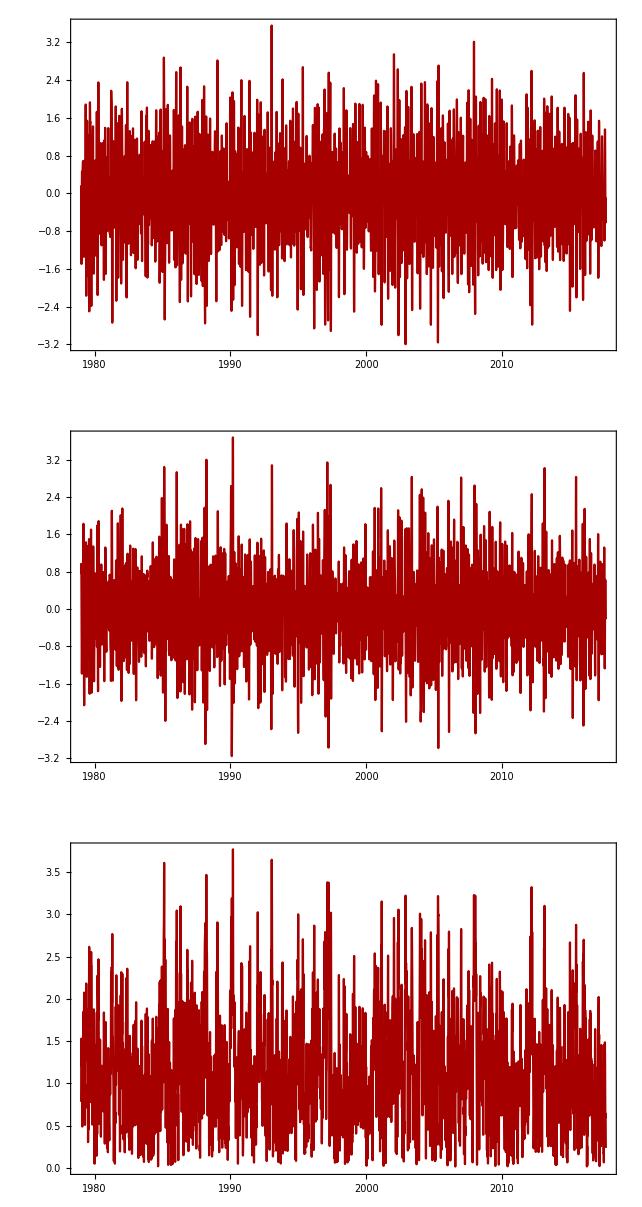

```mathematica
GraphicsColumn[{DateListPlot[TimeSeries[MJO[[;;,5]],{{1979,1,1}}],ImageSize->600],
                DateListPlot[TimeSeries[MJO[[;;,6]],{{1979,1,1}}],ImageSize->600],
                DateListPlot[TimeSeries[MJO[[;;,7]],{{1979,1,1}}],ImageSize->600]}]
```

## Seeking Forecast windows ⟶ ENSO

Given that:

GCMs can capture/predict ENSO

It’s believed that under different phases of ENSO, precipitation for the West Coast United States would be distinct. Specifically:

```mathematica
ENSO=-Graphics-;
LANINA=-Graphics-;
GraphicsRow[Map[ImageResize[ImageCrop[#],500]&,{ENSO,LANINA}],ImageSize->Full]
```

-Graphics-

DIfference from average (1981-2010) winter precipitation (December-February) in each U.S. climate division during strong (dark gray bar), moderate (medium gray), and weak (light gray) El Niño/La Nina events since 1950. Years are ranked based on the maximum seasonal ONI index value observed. During strong El Niño events, the Gulf Coast and Southeast are consistently wetter than average. Maps by NOAA Climate.gov, based on NCDC climate division data provided by the Physical Sciences Division at NOAA ESRL.

We can deduce the following hypotheses:

GCMs can capture/predict ENSO

Implementation

DESCRIPTION: Warm (red) and cold (blue) periods based on a threshold of +/- 0.5oC for the Oceanic Niño Index (ONI) [3 month running mean of ERSST.v5 SST anomalies in the Niño 3.4 region (5oN-5oS, 120o-170oW)], based on centered 30-year base periods updated every 5 years.

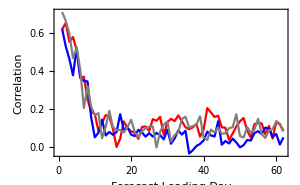
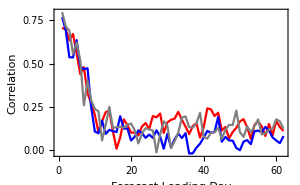
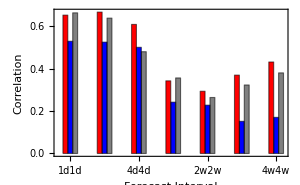
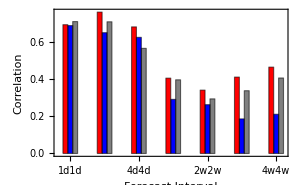
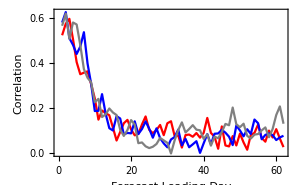
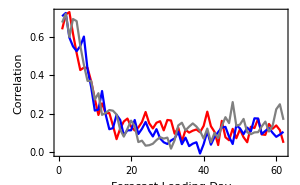
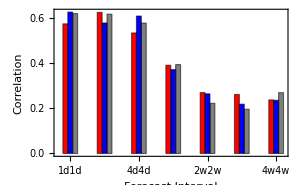
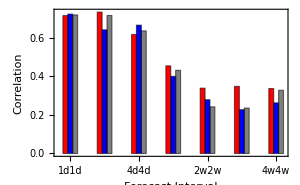
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["BoM"]
```

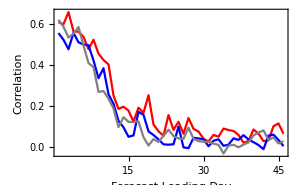
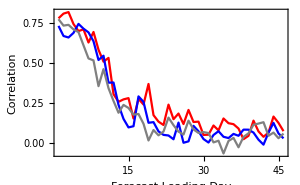
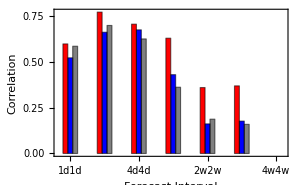
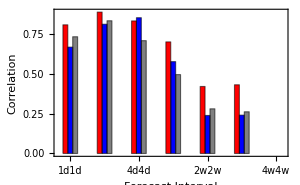
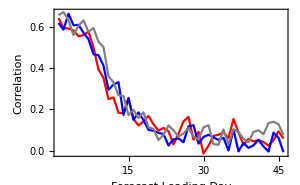
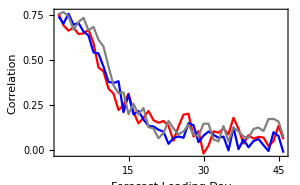
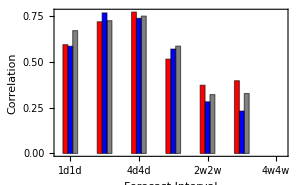
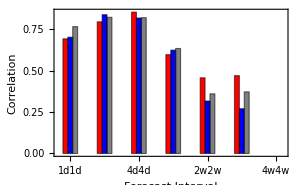
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["ECMWF"]
```

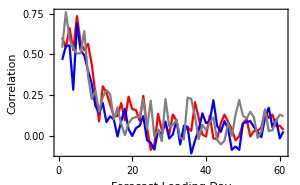
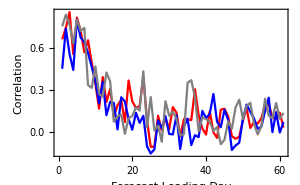
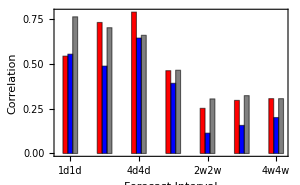
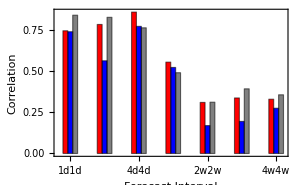
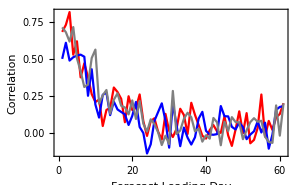
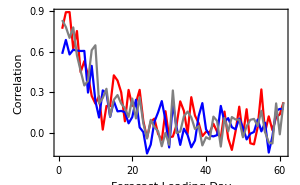
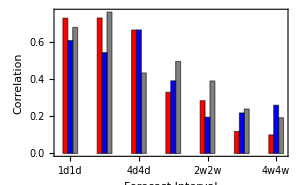
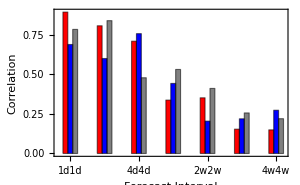
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["MeteoFrance"]
```

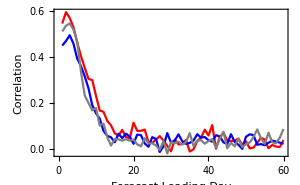
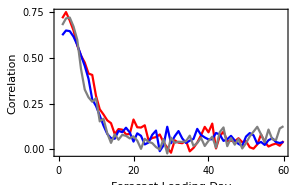
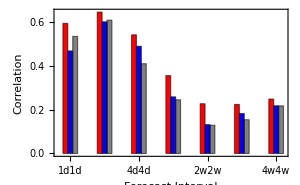
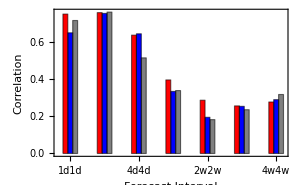
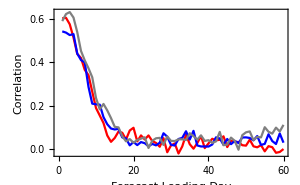
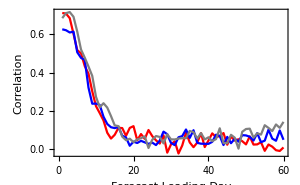
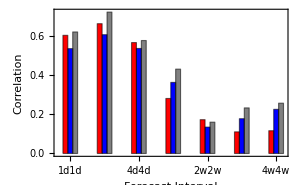
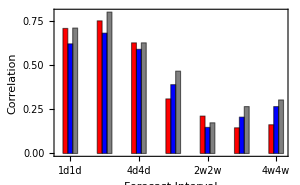
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["CMA"]
```

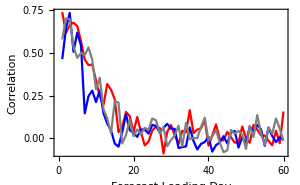
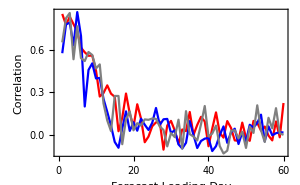
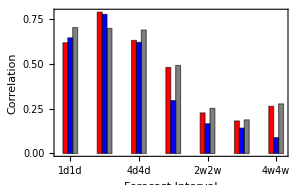
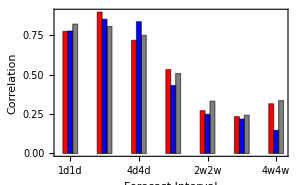
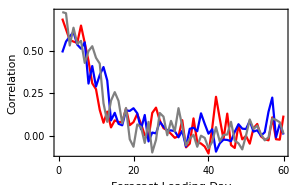
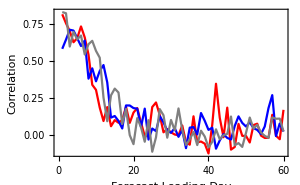
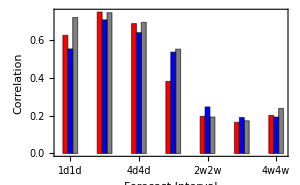
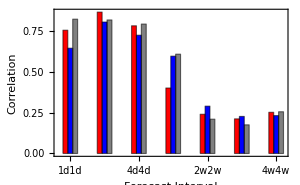
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["UKMO"]
```

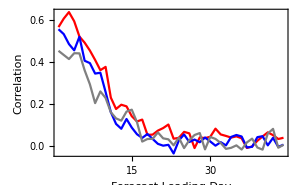
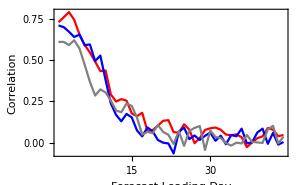
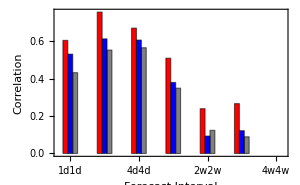
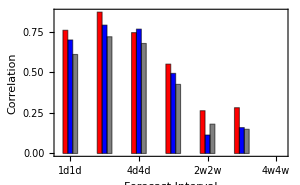
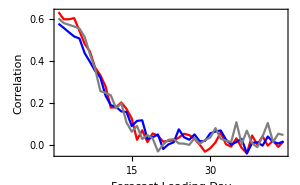
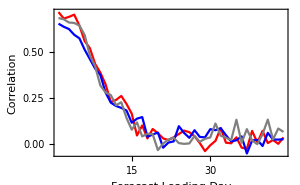
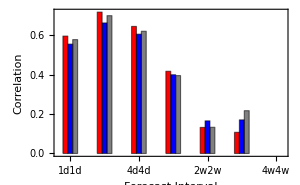
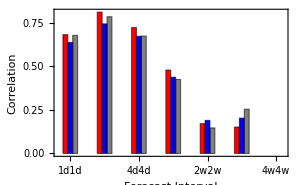
| Grid Daily Scale | Regional Daily Scale | Grid Interval Scale | Regional Interval Scale
SCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
NCA | -Graphics- | -Graphics- | -Graphics- | -Graphics-
OR | -Graphics- | -Graphics- | -Graphics- | -Graphics-
WA | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Visualize["NCEP"]
```

## Conclusion

The quite revolution of numerical prediction has brought

The quiet revolution of numerical weather models has been boosting a consistent increase in accuracy and extension of weather predictions. The progress require keeping clarifying the boundary between weather and climate.  
Extratropical cyclones, storm tracks.

there is never a sharp distincion

The Arctic Oscillation (AO) appears as the leading unrotated mode of principal component analysis (PCA) of monthly mean sea level pressure anomalies, whereas the North Atlantic Oscillation (NAO) results from rotated PCA, regardless of the number of PCs rotated.

#### California Department of Water Resources’s forecast of total April-July river runoff. water-year based indices

USDA Natural Resources Conservation Service in partnership with NOAA/National Weather Service

Snowpack

This work examines the impact of El Niño–Southern Oscillation (ENSO) on the prediction skill of North Pacific variability (NPV) in retrospective predictions of the NCEP Climate Forecast System, version 2. It is noted that the phase relationship between ENSO and NPV at initial conditions (ICs) affects the prediction skill of NPV. For average lead times of 0–6 months, the prediction skills of sea surface temperature anomalies (SSTAs) in NPV (defined as the NPV index) increase from 0.42 to 0.63 from the cases of an out-of-phase relation between the Niño-3.4 and NPV indices in ICs to the cases of an in-phase relation. It is suggested that when ENSO and NPV are in phase in ICs, ENSO plays a constructive role in the NPV development and enhances its signals. Nevertheless, when ENSO and NPV are out of phase, some pronounced positive NPV events are still predictable. In these cases, the North Pacific is dominated by strong positive SSTAs, which may overcome the opposing influence from the tropical Pacific and display predictability.